## 相边界一般性解析解

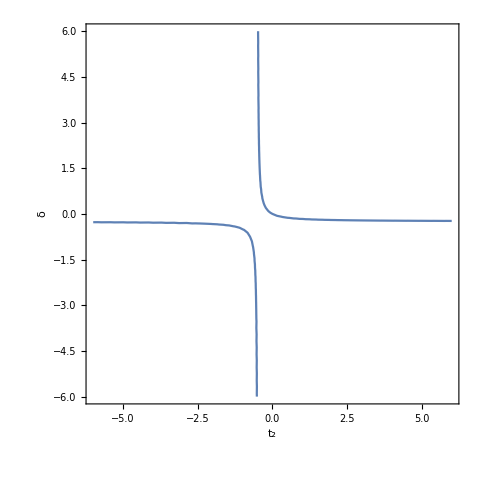

```mathematica
Module[{t1=-1,τ=-1/2},
u=t1+τ;v=t1-τ;
g=ContourPlot[-t2 v+v δ+t2 u+u δ-4t2 δ==0,{t2,-6,6},{δ,-6,6},FrameLabel->{Style[Subscript[t, 2],Large,Bold],Style[δ,Large,Bold]}]
]
```

```mathematica
Module[{t1=-1,τ=-1/2,δ=-5},
u=t1+τ;v=t1-τ;
Solve[-t2 v+v δ+t2 u+u δ-4t2 δ==0,t2]
]
```

{{t2→-10/19}}

## 体能带

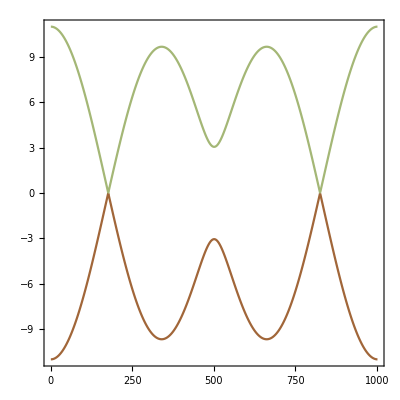

```mathematica
hamiltonian[kx_]:=Module[{tg,tk,ty,tp,h},
tk=t1+τ;
tg=t1-τ;
ty=t2+δ;
tp=t2-δ;
h=Table[0,2,2];
h[[1,2]]=tk+tg*Exp[-ⅈ kx]+tp*Exp[ⅈ kx]+ty*Exp[-2ⅈ kx];
h[[2,1]]=Conjugate@h[[1,2]];
Return[h]
]
el=ParallelTable[Sort@Eigenvalues[hamiltonian[kx]/.{t1->-1,τ->-1/2,t2->-10/19,δ->-5}],{kx,-π,π,0.001*2π}];
ListPlot[Transpose[Re[el]],Frame->True,AspectRatio->1,Joined->True,ColorFunction->"SouthwestColors"]
```

```mathematica
Manipulate[
ContourPlot[-t2 v+δ v+t2 u+δ u-4t2 δ==0,{t2,-6,0},{δ,-6,0},FrameLabel->{Style[Subscript[t, 2],Large,Bold],Style[δ,Large,Bold]}]
,
{u,-2,2},{v,-2,2}]
```